# Parrondo’s paradox and agriculture

## Impact of pathogen

## Enter section title here

#### Enter subsubsection title here

Enter text here. Enter TraditionalForm input for evaluation in a separate cell below:

```mathematica
sqmax=10;
a=1;b=1;
θ=3;
g=1;
pathogenmax=10;
pcovermax=0.4;
p1=0;
p2=0.8;
α=0.5;
```

```mathematica
alldistributions={};
For[α=0,α<=1,α=α+0.5,
meanplots={};
For[γ=0,γ<=1,γ=γ+0.1,
ensemble={};
ensemblepathogen={};
ensemblesoilsq={};
For[j=1,j≤100,j++;
sequence=RandomChoice[{1-γ,γ}->{"cash","cover"},500];
pathogeninit=2;
winninginit=0;
sqinit=0;
Clear[dynamics];
dynamics={{pathogeninit,sqinit,winninginit}};
For[i=1,i≤Length[sequence],i++,
croptype=sequence⟦i⟧;

pathogen=pathogeninit+(Switch[croptype,"cover",If[pathogeninit≤0,0,-g] ,"cash", If[pathogeninit≥pathogenmax,0,g]]);

sq=sqinit+Switch[croptype,"cover",If[sqinit≥sqmax,0,a],
"cash",
If[sqinit≤0,0,-b]
];


winning=winninginit+If[RandomReal[]<Switch[croptype,"cover",pcovermax (1-α pathogeninit/pathogenmax),
"cash",
If[sqinit<θ,p1 (1- α pathogeninit/pathogenmax),
p2 (1-α pathogeninit/pathogenmax)]
],+1,-1];

pathogeninit=pathogen;
sqinit=sq;
winninginit=winning;

AppendTo[dynamics,{pathogeninit,sqinit,winninginit}];
];
AppendTo[ensemble,dynamics⟦All,3⟧];
AppendTo[ensemblepathogen,dynamics⟦All,1⟧];
AppendTo[ensemblesoilsq,dynamics⟦All,2⟧];
];
average=Mean[ensemble];
averagepath=Mean[ensemblepathogen];
averagesq=Mean[ensemblesoilsq];
AppendTo[meanplots,ensemble⟦All,501⟧(*{,ListPlot[average,Joined->True],ListPlot[averagepath,Joined->True],ListPlot[averagesq,Joined->True],ListPlot[{averagepath,averagesq}/10,Joined->True]}*)];
];
AppendTo[alldistributions,meanplots];
]
```

```mathematica
alphas={0,0.5,1.0};
```

```mathematica
Manipulate[SmoothHistogram[Table[Callout[alldistributions⟦i⟧⟦j⟧,"α = "<>ToString[alphas⟦i⟧],Above],{i,1,3,1}],Frame->True,Filling->Axis,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Long term winnings",Black,18]},PlotLabel->Style["Long term winning distributions",Black,18],PlotRange->{{-500,200},Full},Epilog->Inset[Style["γ = "<>ToString[(j-1)/10//N],18,Black],{-400,0.018}]],{j,1,11,1}]
```

```mathematica
Manipulate[SmoothHistogram[Table[Callout[alldistributions⟦j⟧⟦i⟧,"γ = "<>ToString[(i-1)/10//N],Above],{i,2,Length[alldistributions⟦j⟧],1}],Frame->True,Filling->Axis,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Long term winnings",Black,18]},PlotLabel->Style["Long term winning distributions",Black,18],PlotRange->{{-500,200},Full}],{j,1,3,1}]
```

```mathematica
SmoothHistogram[Table[Callout[alldistributions⟦3⟧⟦i⟧,"γ = "<>ToString[(i-1)/10//N],Above],{i,2,Length[alldistributions⟦3⟧],1}],Frame->True,Filling->Axis,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Long term winnings",Black,18]},PlotLabel->Style["Long term winning distributions",Black,18],PlotRange->{{-500,200},Full},AspectRatio->0.5]
```

-Graphics-

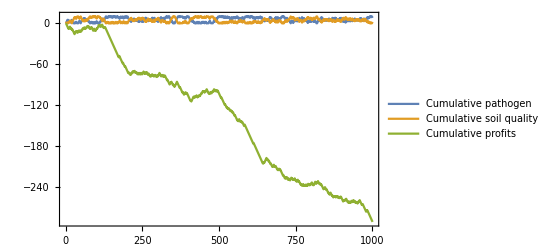

```mathematica
ListPlot[dynamics//Transpose,Joined->True,PlotLegends->{"Cumulative pathogen","Cumulative soil quality","Cumulative profits"},PlotRange->All,Frame->True]
```

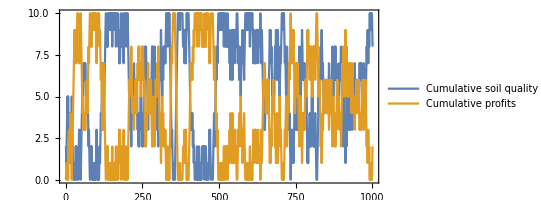

```mathematica
ListPlot[Transpose[dynamics⟦All,1;;2⟧],Joined->True,PlotLegends->{"Cumulative soil quality","Cumulative profits"},AspectRatio->1/2,Frame->True]
```

```mathematica
ensemble⟦1⟧
```

{1,105501}

```mathematica
ListPlot[ensemble,Joined->True,PlotRange->All,Frame->True]
```